Attempting to plot the cross talk for TDM signal

This is the crosstalk as derived by Bennet for simple switches TDM . 
δ is the channel separation (i . e . 1 means neighbors, 2 means one away)
N is the number of channels
ξ is the proportion of time in which we read the signal
M is the highest harmonic of the TDM cycle frequency that the system can handle (i.e. the photodiode bandwidths)
Ylimjk is what the ratio becomes as ξ goes to 0 to be just an infinitesimal point of the segment used

Note that ξ refers to both the multiplex and demultiplex switch
In our case the multiplex ξ should be near 1 since the laser is on for most of the segment (maybe minus the AOD access time so at least > 0.5)
The demultiplex switch ξ is defined by what data we use in the FPGA. Any part cutoff to remove slew rate effects limits how high it can go.
Also it isn’t distributed evenly at the beginning and end which might change it a bit

```mathematica
Yjk[N_,ξ_,δ_][M_] := (1 + 2*∑_(m=1)^M ((Sin[m*Pi*ξ/N]/(m*Pi*ξ/N))^2*Cos[2*m*Pi*δ/N]))/(1+2*∑_(m=1)^M ((Sin[m*Pi*ξ/N]/(m*Pi*ξ/N))^2))
Yassym[N_,χ_,κ_,δ_][M_] := (1 + 2*∑_(m=1)^M ((Sin[m*Pi*χ/N]Sin[m*Pi*κ/N])/(χ*κ*(m*Pi/N)^2)*Cos[2*m*Pi*δ/N]))/(1+2*∑_(m=1)^M ((Sin[m*Pi*χ/N]Sin[m*Pi*κ/N])/(χ*κ*(m*Pi/N)^2)))
Ylimjk[N_,δ_][M_] := Sin[(2M+1)*Pi*δ/N]/((2M+1)Sin[Pi*δ/N])
Ydb [N_,ξ_,δ_][M_] := -10*Log[10,(Yjk[N,ξ,δ][M])^2]
Yassymdb[N_,χ_,κ_,δ_][M_] := -10*Log[10,(Yassym[N,χ,κ,δ][M])^2]
Ylimdb [N_,δ_][M_] := -10*Log[10,(Ylimjk[N,δ][M])^2]
```

Simplifying when M = (N - 1)/2, N is even positive integer for Ylimjk gives 0. Why I cannot say

```mathematica
Ysol[N_,δ_] :=Sin[Pi*δ]/(N*Sin[Pi*δ/N])
```

```mathematica
Trace[Simplify[Sin[Pi*δ]/(N*Sin[Pi*δ/N]), Element[δ, Integers], Assumptions -> Mod[N, 2] == 0]]
```

{{{{{{{δ/N,δ/N},(π δ)/N,(π δ)/N,(π δ)/N},Sin[(π δ)/N]},N Sin[(π δ)/N]},1/(N Sin[(π δ)/N]),Csc[(π δ)/N]/N},(Sin[π δ] Csc[(π δ)/N])/N,(Sin[π δ] Csc[(π δ)/N])/N,(Csc[(π δ)/N] Sin[π δ])/N},{Assumptions→Mod[N,2]==0,Assumptions→Mod[N,2]==0},Simplify[(Csc[(π δ)/N] Sin[π δ])/N,δ∈ℤ,Assumptions→Mod[N,2]==0],0}

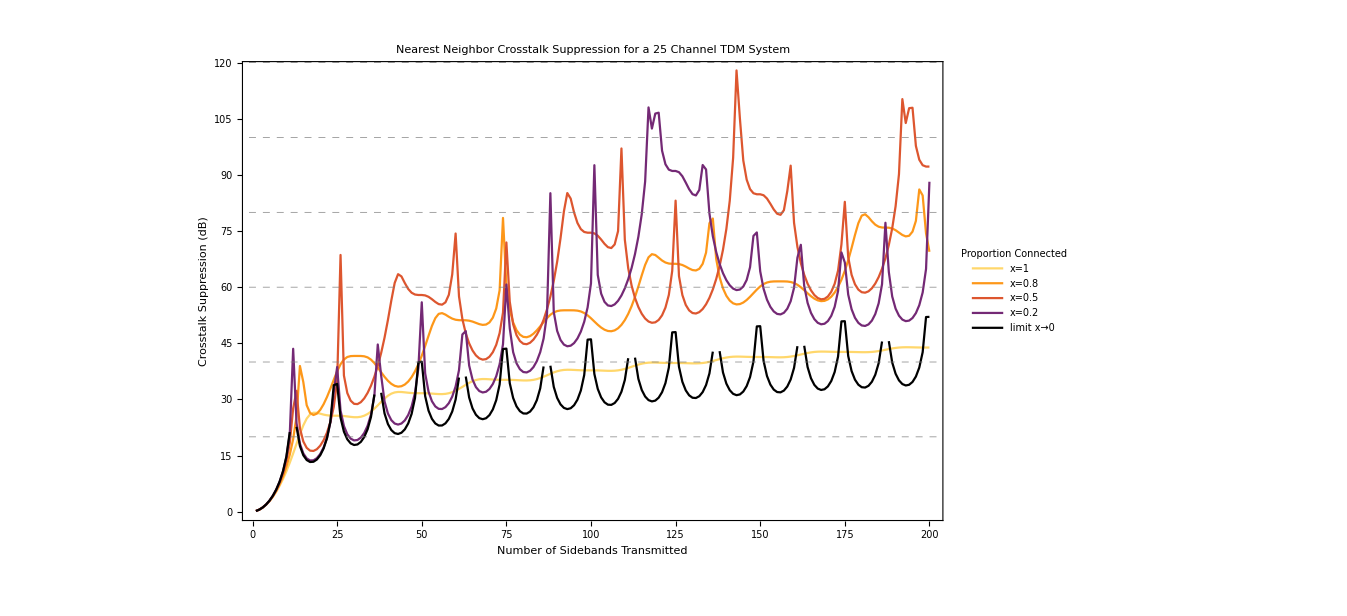

```mathematica
num=25;
colors = Reverse[ColorData["SunsetColors"]/@Range[0,0.8,0.8/4]];
legendlist = {"x=1","x=0.8","x=0.5","x=0.2","limit x→0"};
DiscretePlot[{Ydb[num,1,1][M],Ydb[num,0.8,1][M],Ydb[num,0.5,1][M],Ydb[num,0.2,1][M],Ylimdb[num,1][M]},{M,1,200},
PlotStyle->colors,
Frame-> True,PlotRangePadding->{None,{None,Automatic}},
FrameLabel->{"Number of Sidebands Transmitted","Crosstalk Suppression (dB)"},
LabelStyle->Directive[22,Black,FontFamily->"Sitka Display"],
GridLines->{{},{20,40,60,80,100,120}},GridLinesStyle->Directive[Gray,Dashed],
Filling->False,
PlotLegends->Placed[LineLegend[Automatic,legendlist,Spacings->0.2,LegendFunction->(Framed[#,Background->White]&),LabelStyle->Directive[18,Black,FontFamily->"Times New Roman"],LegendLabel->"Proportion Connected"],{Left,Top}],
PlotLabel->"Nearest Neighbor Crosstalk Suppression for a 25 Channel TDM System"]
```

```mathematica
Export["C:\\Users\\Ben\\Dropbox\\Thesis figures\\crosstalk.pdf",%14,"PDF"]
```

C:\Users\Ben\Dropbox\Thesis figures\crosstalk.pdf

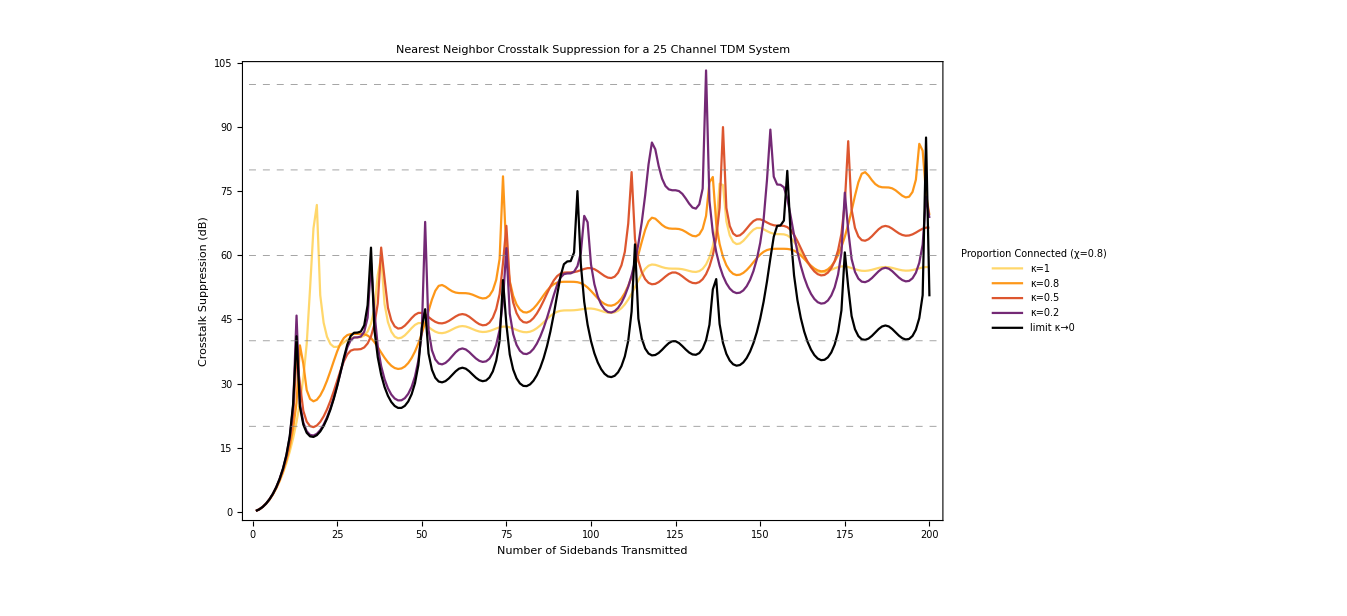

```mathematica
num=25;
colors = Reverse[ColorData["SunsetColors"]/@Range[0,0.8,0.8/4]];
legendlist = {"κ=1","κ=0.8","κ=0.5","κ=0.2","limit κ→0"};
DiscretePlot[{Yassymdb[num,0.8,1,1][M],Yassymdb[num,0.8,0.8,1][M],Yassymdb[num,0.8,0.5,1][M],Yassymdb[num,0.8,0.2,1][M],Yassymdb[num,0.8,0.0001,1][M]},{M,1,200},
PlotStyle->colors,
Frame-> True,PlotRangePadding->{None,{None,Automatic}},
FrameLabel->{"Number of Sidebands Transmitted","Crosstalk Suppression (dB)"},
LabelStyle->Directive[22,Black,FontFamily->"Sitka Display"],
GridLines->{{},{20,40,60,80,100,120}},GridLinesStyle->Directive[Gray,Dashed],
Filling->False,
PlotLegends->Placed[LineLegend[Automatic,legendlist,Spacings->0.2,LegendFunction->(Framed[#,Background->White]&),LabelStyle->Directive[18,Black,FontFamily->"Times New Roman"],LegendLabel->"Proportion Connected\n(χ=0.8)"],{Left,Top}],
PlotLabel->"Nearest Neighbor Crosstalk Suppression for a 25 Channel TDM System"]
```

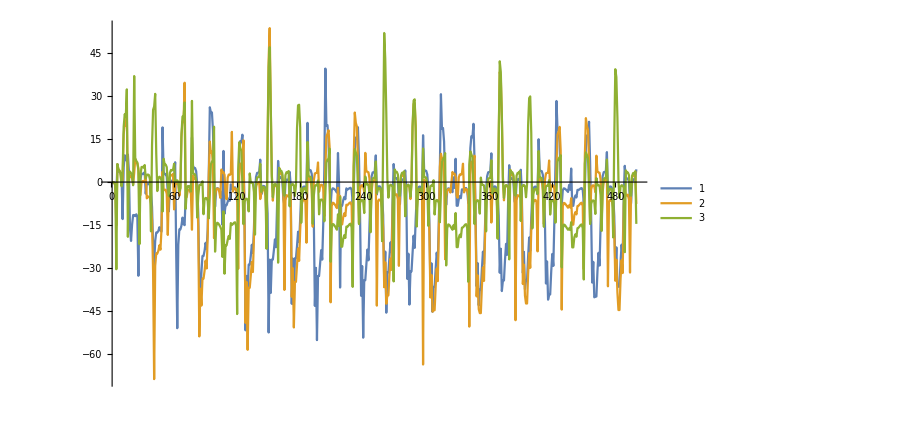

```mathematica
num=11;
legendlist = {"ξ=1","ξ=0.8","ξ=0.5","ξ=0.2","ξ=0.05","limit ξ->0"};
Ydiff[N_,χ_,κ_,δ_][M_] := Yassymdb[N,χ,κ,δ][M] - Ydb[N,κ,δ][M]
DiscretePlot[{Ydiff[num,0.8,0.5,1][M],Ydiff[num,0.8,0.25,1][M],Ydiff[num,0.8,0.1,1][M]},{M,1,500}, Filling->None,Joined->True, PlotLegends->Automatic]
```

Note that while the point sampling method has the worst crosstalk rejection, there are special bandwidths where there is complete cancellation of crosstalk (the undefined parts in the purple line)
Using the entire segment does not result in the best rejection. ξ=0.5 seems to have the best overall performance regardless of bandwidth but other values’ max suppression is better at optimal bandwidths.

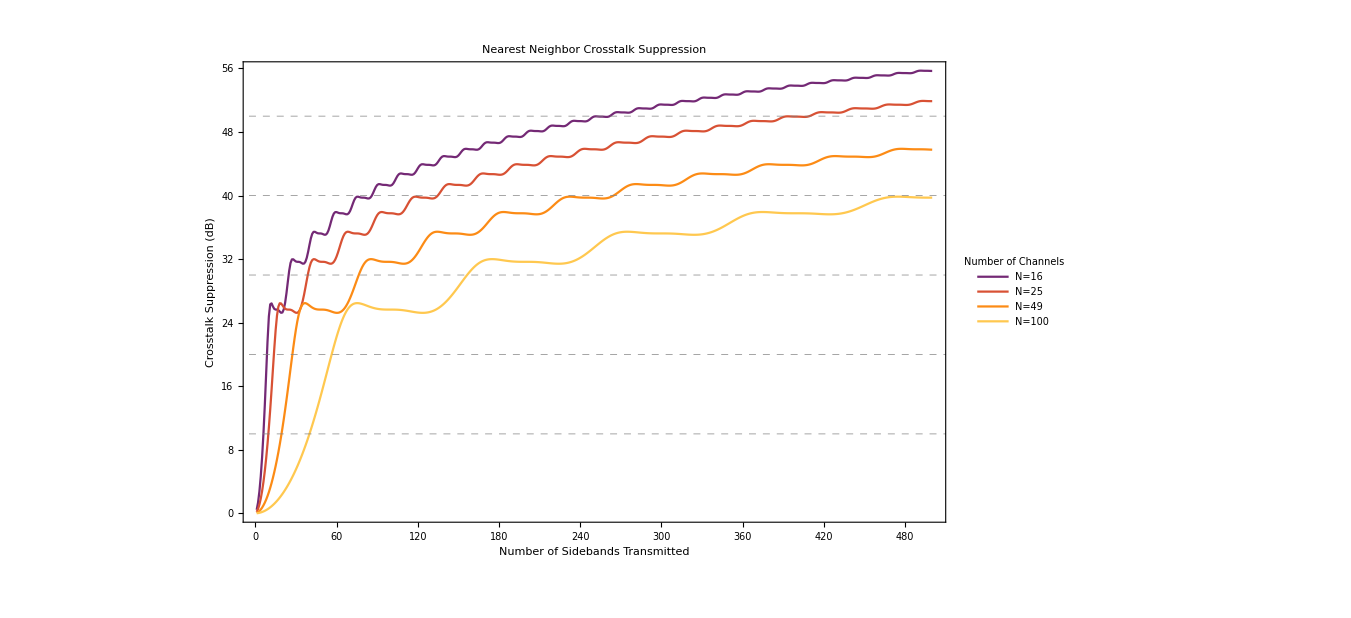

```mathematica
x=1;
colors = ColorData["SunsetColors"]/@Range[0.2,0.75,0.55/3];
legendlist = {"N=16","N=25","N=49","N=100"};
DiscretePlot[{Ydb[16,x,1][M],Ydb[25,x,1][M],Ydb[49,x,1][M],Ydb[100,x,1][M]},{M,1,500},
PlotStyle->colors,
Frame-> True,PlotRangePadding->{None,{None,Automatic}},
FrameLabel->{"Number of Sidebands Transmitted","Crosstalk Suppression (dB)"},
LabelStyle->Directive[22,Black,FontFamily->"Sitka Display"],
GridLines->{{},{10, 20, 30, 40,50}},GridLinesStyle->Directive[Gray,Dashed],
Filling->False,
PlotLegends->Placed[LineLegend[Automatic,legendlist,Spacings->0.2,LegendFunction->(Framed[#,Background->White]&),LabelStyle->Directive[18,Black,FontFamily->"Times New Roman"],LegendLabel->"Number of Channels"],{Right,Bottom}],
PlotLabel->"Nearest Neighbor Crosstalk Suppression"]
```

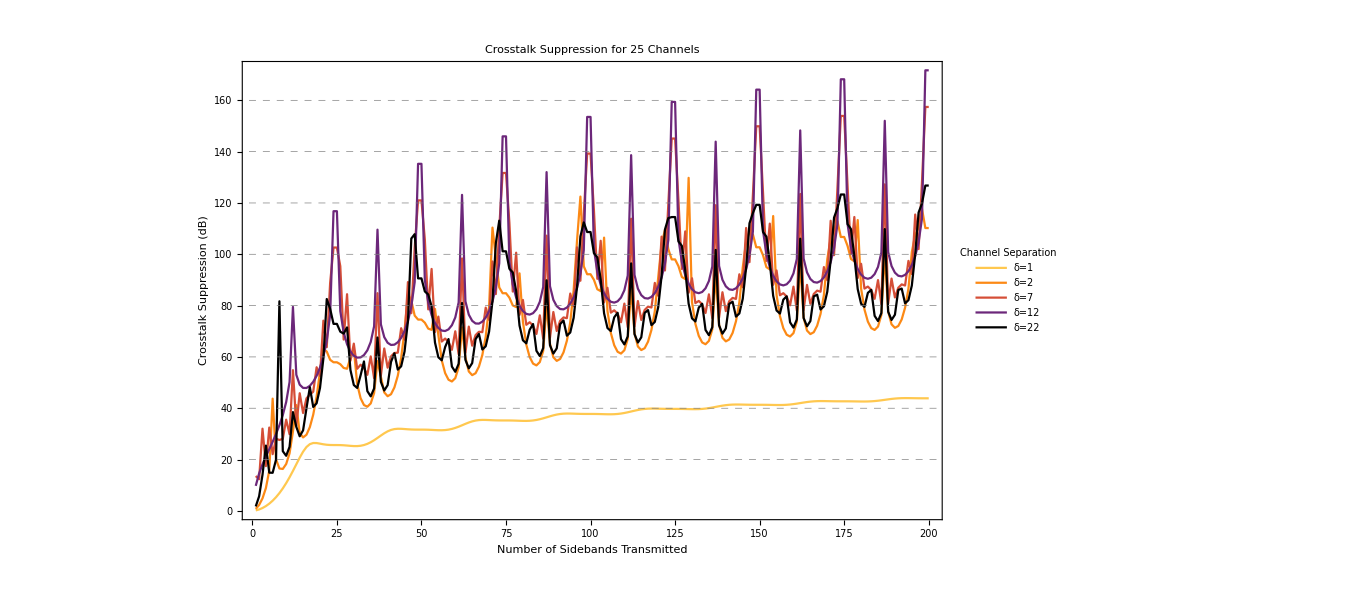

```mathematica
x=1;
Num=25;
colors = Reverse[ColorData["SunsetColors"]/@Range[0,0.75,0.75/4]];
legendlist = {"δ=1","δ=2","δ=7","δ=12","δ=22"};
DiscretePlot[{Ydb[Num,x,1][M],Ydb[Num,x,2][M],Ydb[Num,x,7][M],Ydb[Num,x,12][M],Ydb[Num,x,22][M]},{M,1,200},
PlotStyle->colors,
Frame-> True,PlotRangePadding->{None,{None,None}},
FrameLabel->{"Number of Sidebands Transmitted","Crosstalk Suppression (dB)"},
LabelStyle->Directive[22,Black,FontFamily->"Sitka Display"],
GridLines->{{},{20,40,60,80,100,120,140,160}},GridLinesStyle->Directive[Gray,Dashed],
Filling->False,
PlotLegends->Placed[LineLegend[Automatic,legendlist,Spacings->0.15,LegendFunction->(Framed[#,Background->White]&),LabelStyle->Directive[18,Black,FontFamily->"Times New Roman"],LegendLabel->"Channel Separation"],{Left,Top}],
PlotLabel->"Crosstalk Suppression for 25 Channels"]
```

```mathematica
num=10
DiscretePlot3D[Ydb[num,ξ/100,1][M],{ξ,0,100,10},{M,1,100,1}]
```

10

-Graphics3D-